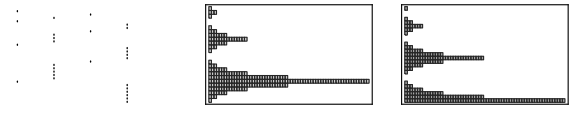

```mathematica
RMCompile[_->z:{_,_,1}]:=RMCompile0[z,{1,2}];
RMCompile[_->z:{_,_,-1}]:=RMCompile0[z,{2,1}];
RMCompile0[{s_,a_,_},{ra_,rb_}]:=Flatten[{i[3],dr[ra,-1],dr[3,3],i[ra],i[ra],dr[3,-2],If[a==1,i[ra],{}],i[3],dr[rb,5],i[rb],dr[3,-1],dr[rb,1],dm[rb,{s,0}],dr[rb,-6],i[rb],dr[3,-1],dr[rb,1],dm[rb,{s,1}]}];

TMToRM[rules_]:=Module[{subs,adrs},subs=RMCompile/@rules;adrs=Thread[First/@rules->Most[FoldList[Plus,1,Length/@subs]]];MapIndexed[#1/.{dr[r_,n_]:>d[r,n+First[#2]],dm[r_,z_]:>d[r,z/.adrs]}&,Flatten[subs]]/.<|i->List,d->List|>];

RMStep[prog_,state:{Halted,_List}]:=state;
RMStep[prog_,{instr_Integer,regs_List}]:=If[instr>Length[prog],{Halted,regs},With[{t=prog[[instr]]},If[Length[t]==1,{instr+1,MapAt[#1+1&,regs,First[t]]},If[regs[[First[t]]]==0,{instr+1,regs},{Last[t],MapAt[#1-1&,regs,First[t]]}]]]];

RMEvolveList[prog_,regs_,n_Integer]:=NestList[RMStep[prog,#]&,{1,regs},n];

RMGraphics[prog_List,history_]:=With[{states=history[[All,1]],regs=Transpose[history[[All,2]]]},GraphicsRow[{Graphics[MapIndexed[Disk[{#1,-First[#2]},.35]&,states],],,Splice[With[{gfun=Interpolation[{{1,.8},{Length[regs],.5}},InterpolationOrder->1]},MapIndexed[Graphics[{EdgeForm[GrayLevel[.15]],GrayLevel[gfun[First[#2]]],MapIndexed[Table[Rectangle[{i,-First[#2]}],{i,#}]&,#]},PlotRange->{{1,Automatic},{-Length[#1],0}},PlotRangePadding->{{0,Max[regs]/4},0},Frame->True,FrameTicks->False,ImagePadding->0]&,regs]]]},]];

With[{rule=TMToRM[{{1,0}->{2,1,-1},{1,1}->{1,1,1},{2,0}->{1,1,1},{2,1}->{2,1,-1}}]},RMGraphics[rule,#[[With[{p=Flatten[Position[#,{_,{_,_,0}}]]},Complement[p,p-1][[;;;;2]]]]]&@RMEvolveList[rule,{0,0,0},1800]]]
```